```mathematica
relu[A_]:=MapThread[Max,{Array[0&,Dimensions@A],A},Length[Dimensions[A]]];
nrelu[A_]:=MapThread[Min,{Array[0&,Dimensions@A],A},Length[Dimensions[A]]];
reluDot[A_,B_]:=relu[A.B];
nreluDot[A_,B_]:=nrelu[A.B];
```

```mathematica
deploy
```

CloudObject[]

```mathematica
asdf=%
```

CloudObject[]

## Equation setup

```mathematica
(* Globals:
lossEq: equation for loss
errEq: equation for error
gradEq: equation for gradient
hessEq: equation for Hessian
pre0: dummy preconditioner
n: number of layers
dsize: number of datapoints, aka f[-1]
fs: list of sizes
f[i]: gives dims, f[i],f[i-1] is dimension of layer i
W[i,j]: W[i].W[i-1]..W[j]
U[i,j]: U[i].U[i+1]...U[j]
makeW[i]: creates matrix of form {{W[i][1,1],W[i][1,2],...
Y: contains array of outputs
vars: contains all W's except W0 (same as X)
allvars: contains all W's
A[i],B[i],B[i].A[i]ᵀ define activation, backprop, gradient for layer i
Bn[i] truncated backprop for Newton's method
hessBlock[i,j] gives Hessian of layer i with respect to layer j
hess[i,j] gives Mathematica derived Hessian of layer i with respect to layer j
gradBlock[i] gives gradient at layer i
grad[i]: gives Mathematica gradient of layer i
sub1: replaces all W's and Y's with 1's
subr: replaces all W's and Y's with fixed random-looking number
*)

(* Number of features per layer *)
(* Number of layers, aka number of matmuls *)
(* f[i] shorthand for shape, W[i] has dimensions f[i]xf[i-1] *)
(* f[-1] is shorthand for dsize *)
Unprotect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];
Clear[lossEq,errEq,gradEq,hessEq,n,dsize,W,U,makeW,Y,X,vars,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

fs={4,2,2,2};
n=Length[fs]-2;
Block[{i},For[i=1, i≤Length[fs],i++,f[i-2]=fs[[i]]]];
dsize=f[-1];

(* TODO: seal flatten/unflatten *)
Unprotect[flatten,unflatten];
flatten[Ws_]:=c2v[vec/@Ws];
unflatten[Wf_]:=Module[{flatVars,sizes},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvec[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];
Protect[flatten,unflatten];

makeW[k_]:=Array[W[k],{f[k],f[k-1]}];
vars=Table[makeW[k],{k,1,n}]; (* W1, W2, ..., Wn *)
Wf=flatten@vars;
allvars=Table[makeW[k],{k,0,n}]; (* W0, W1, W2, ..., Wn *)

Y=Array[y,{f[n],f[-1]}];
X=makeW[0];

(* todo: add predeq, predf to protected symbols *)
predEq=reluDot[makeW[2],reluDot[makeW[1],makeW[0]]];
errEq=Y-predEq;
lossEq=1/2Tr[errEqᵀ.errEq]/dsize;
gradEq=D[lossEq,{Wf,1}];
hessEq=D[lossEq,{Wf,2}];
pre0=IdentityMatrix[Length@Wf];

(* Partial products. Shorthand notation for doing product of all layers between j and i (inclusive). W refers to original sums and U is transpose *)

(* W[i,j]=W[j].W[j-1]...W[i] *)
W[bottom_,top_]:=IdentityMatrix[f[bottom]]/;bottom<top;
W[bottom_,top_]:=Module[{sublist},
Assert[top≤bottom,"W ordering"];
sublist=allvars[[top+1;;bottom+1]];
Fold[Dot,Reverse@sublist]
];

(* U[i,j]=U[i].U[i+1]...U[j] *)
U[bottom_,top_]:=IdentityMatrix[f[top]]/;bottom>top
U[bottom_,top_]:=Module[{sublist},
Assert[bottom≤top,"U ordering"];
sublist=Transpose/@allvars[[bottom+1;;top+1]];
Fold[Dot,sublist]
];

(* Activation at layer i. Defines derivative for layer i. A[0]=Identit[dsize] *)
A[i_]:=W[i-1,0];          

(* Backprop at layer i. Defines derivative for layer i. B[n]=d_error *)
B[i_]:=-U[i+1,n].errEq/dsize;

(* Partial products needed for Newton's method *)
Bn[i_]:=U[i+1,n];

hessBlock[i_,j_]:=Module[{term1,term2},
term1=(A[i].A[j]ᵀ)⊗(Bn[i].Bn[j]ᵀ)/dsize;
Assert[Dimensions@term1=={f[i]*f[i-1],f[j]*f[j-1]}];
term2=Which[
i==j,Array[0&,Dimensions[term1]],
i<j,(A[i].B[j]ᵀ)⊗U[i+1,j-1],
i>j,U[j+1,i-1]ᵀ⊗(B[i].A[j]ᵀ)
];
(term1+term2.Kmat[f[j],f[j-1]])
];

gradBlock[i_]:=c2v@vec[B[i].A[i]ᵀ];

(* substitutes 1 to every variable *)
sub1:=Module[{},
everything=Flatten[vec/@allvars]~Join~c2v@vec@Y;
Thread[everything->Array[1&,Length@everything]]
];

(* substitutes random value to every variable *)
subr:=Module[{},
SeedRandom[0];
everything=Flatten[vec/@allvars]~Join~c2v@vec@Y;
Thread[everything->RandomReal[{-1,1},Length@everything]]
];

(* Functional versions of equations *)
predF[W_]:=predEq/.subX/.subY/.subW[W];
errF[W_]:=errEq/.subX/.subY/.subW[W];
lossF[W_]:=lossEq/.subX/.subY/.subW[W];
gradF[W_]:=gradEq/.subX/.subY/.subW[W];
hessF[W_]:=hessEq/.subX/.subY/.subW[W];

(* Run checks *)
grad[i_]:=Module[{},Assert[i≥0 && i≤n,"grad i check"];
D[lossEq,{c2v@vec@allvars[[i+1]],1}]];

hess[i_,j_]:=Module[{},Assert[j≥0&&j≤n,"hess j check"];
D[grad[i],{c2v@vec@allvars[[j+1]],1}]];

Protect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

idx=Range[n+1]-1; (* all valid layer indices, including W0 *)
blockIdx=Outer[List,idx,idx];

(* Checks correctness of block i,j *)
hessCheck[i_,j_]:=hess[i,j]≐hessBlock[i,j]/.subr;
gradCheck[i_]:=grad[i]==gradBlock[i]/.subr;
gradCheck/@idx
Apply[hessCheck, blockIdx,{2}]//MatrixForm
```

{False,False,False}

(False | False | False
False | False | False
False | False | False)

## Data setup

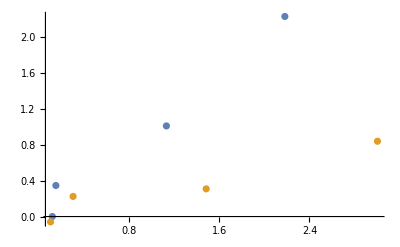

```mathematica
generateX[n_,e_,dsize_]:=Module[{wt,mean,cov,normal,X},
SeedRandom[4];
mean=Table[0,{n}];
cov=IdentityMatrix[n]*e+Array[1-e&,{n,n}];
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
centerData[X]
];
X0=generateX[f[0],0.01,dsize];
X0=X0-Min[X0];  (* generate positive X *)
θ0=-Pi/6; (* rotate in negative dimension so that some points are impossible *)
Y0=RotationMatrix[θ0].X0;
Export["~/git/whitening/exp/data/rotations_relu_X0.csv",X0];
Export["~/git/whitening/exp/data/rotations_relu_Y0.csv",Y0];

makeInitializer[k_]:=truncatedIdentity[f[k],f[k-1]];
W0s=Table[makeInitializer[k],{k,1,n}];
W0f=flatten@W0s;
Export["~/git/whitening/exp/data/rotations_relu_W0f.csv",W0f];
Export["~/git/whitening/exp/data/rotations_relu_fs.csv",fs];

(* Todo: refactor into helper functions *)
subX:=Thread[Flatten@X->Flatten@X0];
subY:=Thread[Flatten@Y->Flatten@Y0];
subW[Wfval_]:=(Assert[Length@Wfval==Length@Wf];Thread[Wf->Wfval]);
subW0:=subW[W0f];
ListPlot[{X0ᵀ,Y0ᵀ},PlotRange->All]
```

## Optimizer setup

```mathematica
(* Applies single step of optimization *)
step[x_,lr_,pre_,grad_,lossFunc_]:=Module[{},
pointsList=pointsList~Append~x;
gradList=gradList~Append~grad;
preList=preList~Append~pre;
lossList=lossList~Append~lossFunc[x];
x-lr*pre.grad
];
resetStep:=({pointsList, gradList,preList, lossList}={{},{},{},{}};W0f);
```

## Optimizer experiments

### Gradient Descent

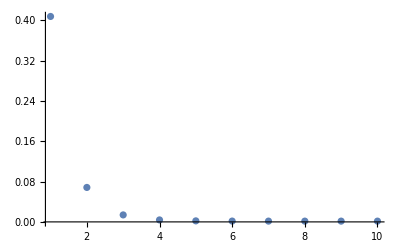

```mathematica
optimizeGradient[.1,10];
Export["~/git/whitening/exp/data/rotations_relu_gradient_losses.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

### Newton' s method

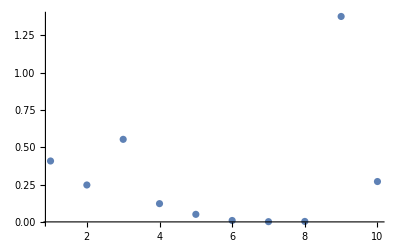

```mathematica
Export["~/git/whitening/exp/data/rotations_relu_newton_hess0.csv",hessF[W0f]];
optimizeNewton[1.,10];
Table[reluDot[makeW[2],reluDot[makeW[1],makeW[0]]]/.subW[point]/.subX,{point,pointList}];
Export["~/git/whitening/exp/data/rotations_relu_newton_losses.csv",lossList];
ListPlot[lossList,PlotRange->All]
```